Reproduce Ogasawara et al. [2017] plots, make sure they real

### The function, equation (1)

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_,mass_]:=n (mass/(2 π kappa T (1-3/(2 kappa))))^(3/2)2/mass^2 Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

#### After Spence has had his way

n in cm^-3
T in keV
energy in keV
phi0 in keV

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

Energy “pre-shifted” by phi0

```mathematica
OgasaFuncShift[en_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

### Parameters for Arc1

```mathematica
phi0=83/10; (*kV*)
T=14/10; (*keV*)
n=6/10; (*cm^-3*)
kappa=21;
```

```mathematica
fluxdivE={1*^7,7*^6,1.2*^6,6*^5,1.5*^5,5*^4,1.9*^4,1.2*^3,8*^1,9,4};
EminusPhi={2,4,6,7.5,9,11,13,18,21,31,39};
```

```mathematica
obs=Partition[Riffle[EminusPhi,fluxdivE],2]
```

{{2,10000000},{4,7000000},{6,1.2×10^6},{7.5,600000},{9,150000.},{11,50000},{13,19000.},{18,1200.},{21,80},{31,9},{39,4}}

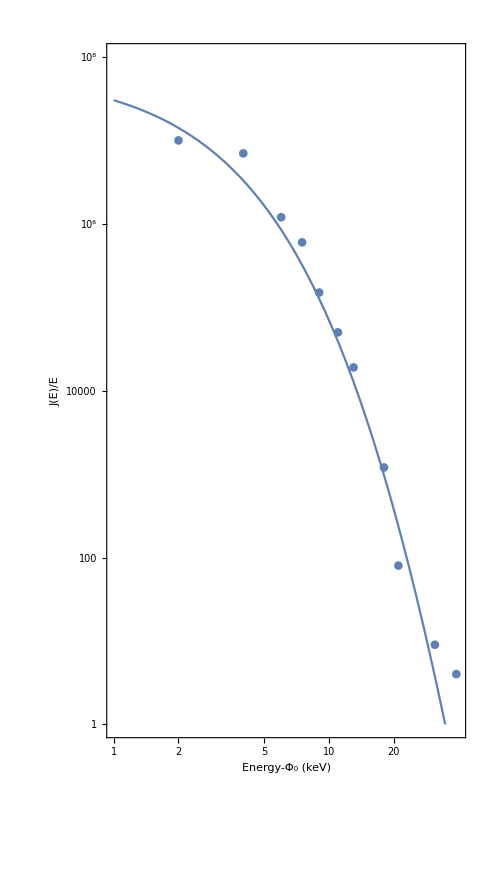

```mathematica
Show[LogLogPlot[OgasaFuncShift[en,T,kappa,n],{en,1,40},PlotRange->{{1,40},{1,1*^8}},Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300],ListLogLogPlot[obs]]
```

### Data from my arc

Function to situate things nicely

```mathematica
makeErrorBPlotPackage[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
errorB=Map[ErrorBar,errorsDivE];
zeList=Partition[Riffle[eAndFlux,errorB],2]
];
```

```mathematica
makeErrorBPlotPackage2[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
zeList=Partition[Flatten[Riffle[eAndFlux,errorsDivE]],3]
];
```

```mathematica
(*energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,1.806*^4,2.208*^4,2.609*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,0.000,6.748,0.000,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,0.000,4.772,0.000,2.489};*)
```

```mathematica
energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,2.208*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,6.748,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,4.772,2.489};
```

```mathematica
eFandError=makeErrorBPlotPackage[energies,flux/energies,errors/energies]
```

{{{815.4,872.333},ErrorBar[32.7447]},{{940.8,770.089},ErrorBar[26.6688]},{{1129.,391.054},ErrorBar[15.837]},{{1380.,122.754},ErrorBar[7.25362]},{{1631.,37.8725},ErrorBar[3.40773]},{{1882.,13.305},ErrorBar[1.7492]},{{2258.,4.57042},ErrorBar[0.846324]},{{2760.,1.39638},ErrorBar[0.383333]},{{3261.,0.685986},ErrorBar[0.224992]},{{3763.,0.331119},ErrorBar[0.133829]},{{4516.,0.094907},ErrorBar[0.0536537]},{{5519.,0.0757202},ErrorBar[0.0373075]},{{6523.,0.0297103},ErrorBar[0.0194236]},{{7526.,0.01443},ErrorBar[0.00859819]},{{9032.,0.00365035},ErrorBar[0.00249225]},{{11040.,0.00181522},ErrorBar[0.00146105]},{{13050.,0.000440153},ErrorBar[0.000440153]},{{15050.,0.000330764},ErrorBar[0.000330764]},{{18060.,0.},ErrorBar[0.]},{{22080.,0.000305616},ErrorBar[0.000216123]},{{26090.,0.},ErrorBar[0.]},{{30110.,0.0000826636},ErrorBar[0.0000826636]}}

```mathematica
Needs["ErrorBarPlots`"]
```

#### Now a function for FAST

n in cm^-3
T in eV
Φ_0 in eV
en in eV

```mathematica
OgasaFuncFAST[en_,phi0_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
OgasaFuncFASTShift[en_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
showError=0;
```

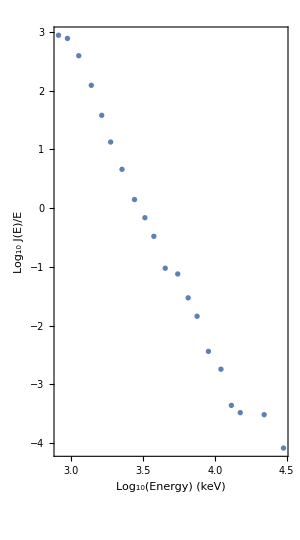

```mathematica
ErrorListPlot[makeErrorBPlotPackage[Log10[energies],Log10[flux/energies],Log10[errors/energies*showError]],Frame->True,FrameLabel->{"Log_10(Energy) (keV)","Log_10 J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300]
```

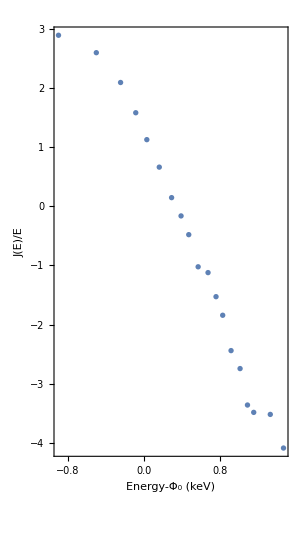

```mathematica
ErrorListPlot[makeErrorBPlotPackage[Log10[(energies-(energies[[1]]))/1000],Log10[flux/energies],Log10[errors/energies*showError]],Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300]
```

```mathematica
(*dataWithError={{0.0333333,0.0000122672,0.00000173485},{0.05,0.0000371462,0.00000448037},{0.0666667,0.0000697768,0.00000748151},{0.0833333,0.000108625,0.000010837},{0.1,0.000147595,0.0000136051},{0.116667,0.000186599,0.0000161483},{0.133333,0.000221451,0.0000179078},{0.15,0.000253062,0.0000192494}};*)
```

```mathematica
dataWithError=makeErrorBPlotPackage2[energies,flux/energies,errors/energies]
```

{{815.4,872.333,32.7447},{940.8,770.089,26.6688},{1129.,391.054,15.837},{1380.,122.754,7.25362},{1631.,37.8725,3.40773},{1882.,13.305,1.7492},{2258.,4.57042,0.846324},{2760.,1.39638,0.383333},{3261.,0.685986,0.224992},{3763.,0.331119,0.133829},{4516.,0.094907,0.0536537},{5519.,0.0757202,0.0373075},{6523.,0.0297103,0.0194236},{7526.,0.01443,0.00859819},{9032.,0.00365035,0.00249225},{11040.,0.00181522,0.00146105},{13050.,0.000440153,0.000440153},{15050.,0.000330764,0.000330764},{22080.,0.000305616,0.000216123},{30110.,0.0000826636,0.0000826636}}

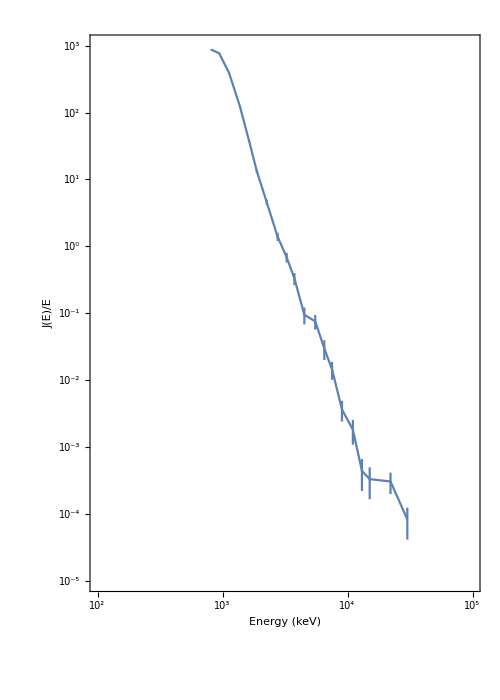

```mathematica
plotrange={Floor@Log10@Min[#],Ceiling@Log10@Max[#]}&@dataWithError[[All,#]]&/@{1,2};
logData={{Log10[#[[1]]],Log10[#[[2]]]},ErrorBar[Log10[1+0.5#]&/@{-#[[3]]/#[[2]],#[[3]]/#[[2]]}]}&/@dataWithError;
xticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[1]];
yticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[2]];
{xt,yt}=#~Join~({#,""}&/@Flatten[(#[[1]]+Log10[{2,3,4,5,6,7,8,9}])&/@#])&/@{xticks,yticks};

ErrorListPlot[logData,Joined->True,PlotRange->plotrange,FrameTicks->{{yt,None},{xt,None}},Frame->True,Axes->False,FrameLabel->{"Energy (keV)","J(E)/E"},FrameStyle->(FontSize->18),AspectRatio->14/10,ImageSize->500]
```